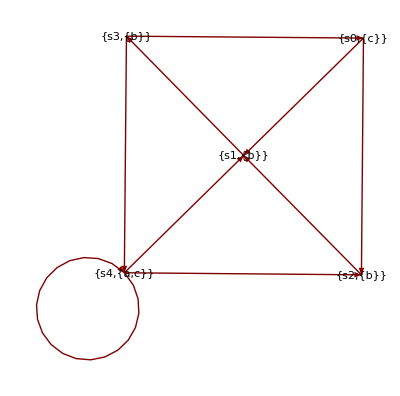

```mathematica
GetInputVertex[transitions_,index_]:=transitions[[index,1,1]];
GetOutputVertex[transitions_,index_]:=transitions[[index,1,2]];
GetWeight[transitions_,index_]:=transitions[[index,2]];
GetOutputVertices[transitions_,vertexName_]:=
(
result={};
For[i=1,i≤Length[transitions],++i,
If[GetInputVertex[transitions,i]==vertexName,
AppendTo[result,{GetOutputVertex[transitions,i],GetWeight[transitions,i]}];
];
];
Return[result];
);
s0={"s0",{c}};
s1={"s1",{b}};
s2={"s2",{b}};
s3={"s3",{b}};
s4={"s4",{a,c}};
transitions={{s0->s1,0.8},{s0->s2,0.2},{s1->s3,1},{s2->s1,1},{s3->s0,0.2},{s3->s4,0.8},{s4->s1,0.1},{s4->s2,0.4},{s4->s4,0.5}};
GraphPlot[transitions,DirectedEdges->True,VertexLabeling->True]
```

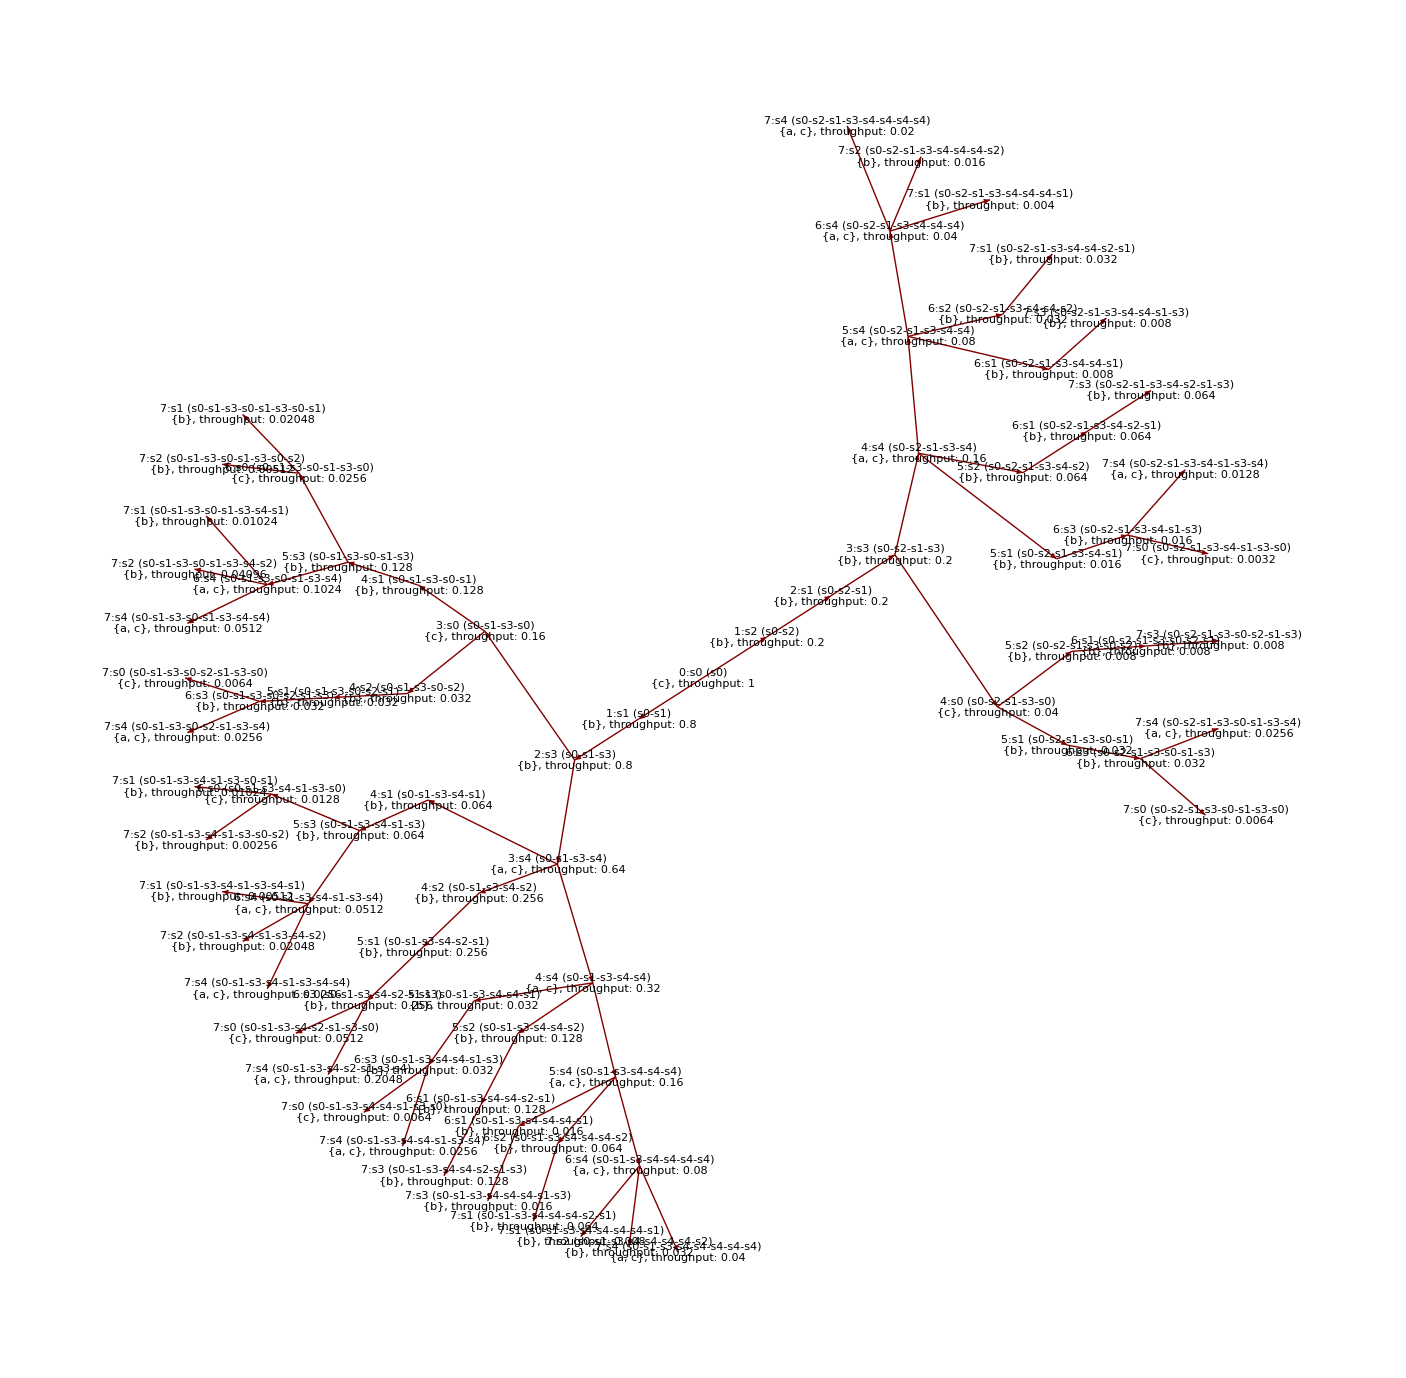

```mathematica
stack={};
Push[x_]:=(AppendTo[stack,x]);
Pop[]:=(stack=Drop[stack,-1]);
StackTop[]:=stack[[-1]];

GetVertexName[vertex_]:=vertex[[1]];
GetVertexState[vertex_]:=ToString[vertex[[2]]];

UnfoldGraph[startVertex_]:=(
unfolded={};
Push[{startVertex,0,"s0",1}];
While[Length[stack]>0,
top=StackTop[];
currentVertex=top[[1]];
depth=top[[2]];
history=top[[3]];
throughput=top[[4]];
Pop[];
outVertices=GetOutputVertices[transitions,currentVertex];
For[outIdx=1,outIdx≤Length[outVertices],++outIdx,
outVertex=outVertices[[outIdx,1]];
outWeight=outVertices[[outIdx,2]];
newThroughput=throughput*outWeight;
newHistory=history<>"-"<>GetVertexName[outVertex];
If[depth<6,
Push[{outVertex,depth+1,newHistory,newThroughput}];
];
AppendTo[unfolded,{ToString[depth]<>":"<>GetVertexName[currentVertex]<>" ("<>history<>")\n"<>GetVertexState[currentVertex]<>", throughput: "<>ToString[throughput]->ToString[depth+1]<>":"<>GetVertexName[outVertex]<>" ("<>newHistory<>")\n"<>GetVertexState[outVertex]<>", throughput: "<>ToString[newThroughput],outWeight}
];

];
];
Return[unfolded];
)

res=UnfoldGraph[s0];
GraphPlot[res,DirectedEdges->True,VertexLabeling->True]
```

```mathematica
GetOutputVertices[transitions,s0][[1,2]]
```

0.8

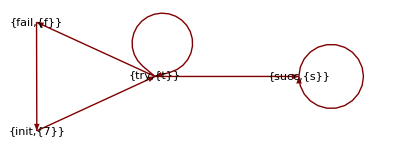

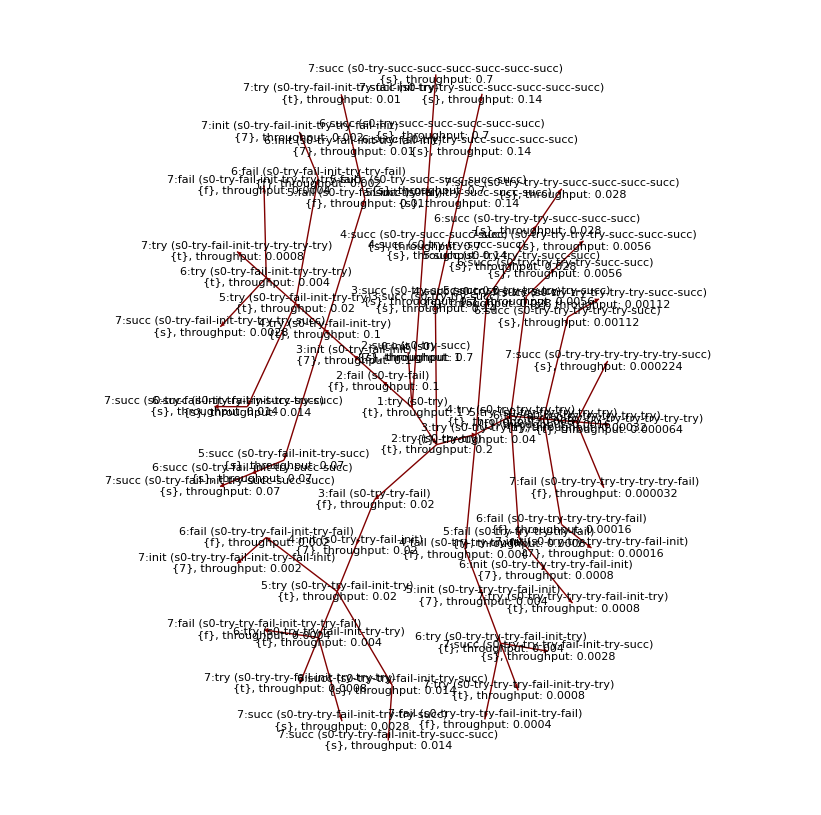

```mathematica
init={"init",{i}};
try={"try",{t}};
fail={"fail",{f}};
succ={"succ",{s}};
transitions={{init->try,1},{try->fail,0.1},{try->try,0.2},{try->succ,0.7},{fail->init,1},{succ->succ,1}};
GraphPlot[transitions,DirectedEdges->True,VertexLabeling->True]
res=UnfoldGraph[init];
GraphPlot[res,DirectedEdges->True,VertexLabeling->True]
```